```mathematica
OS="win";(*or linux*)
Needs["ErrorBarPlots`"];
Needs["EDA`"];
Needs["PhysicalConstants`"];
ch=PlanckConstant/(Joule Second);
If[OS=="win",
Print["Working Directory: ",curDir=SetDirectory["C:\\Users\\Prajwal\\Dropbox\\nEDM\\nedm-analysis\\analysis"]];
Print["(ASCII) Rawdata Directory: ",AscDir="C:\\Users\\Prajwal\\Dropbox\\nEDM\\rawdata"];
];
If[OS=="linux",
Print["Working Directory:",curDir=SetDirectory["/home/prajwal/Dropbox/nEDM/nedm-analysis/analysis"]];
Print["(faster) Rawdata Directory:",fastDir="/home/prajwal/nEDM/rawdata"];
Print["(ASCII) Rawdata Directory:",AscDir="/home/prajwal/Dropbox/nEDM/rawdata"];
];
Print["Runs in the list: ",runNum={10251,10288}];
metaStructure={Word,Real,Real,Word,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real};
dimdata=Table[{0,0},{k,1,Dimensions[runNum][[1]]}];
```

General::obspkg: "PhysicalConstants`" is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

Working Directory: C:\Users\Prajwal\Dropbox\nEDM\nedm-analysis\analysis

(ASCII) Rawdata Directory: C:\Users\Prajwal\Dropbox\nEDM\rawdata

Runs in the list: {10251,10288}

```mathematica
nupp01={0.};nupp02={0.};nupp11={0.};nupp12={0.};
nupn01={0.};nupn02={0.};nupn11={0.};nupn12={0.};
nupz01={0.};nupz02={0.};nupz11={0.};nupz12={0.};
ndownp01={0.};ndownp02={0.};ndownp11={0.};ndownp12={0.};
ndownn01={0.};ndownn02={0.};ndownn11={0.};ndownn12={0.};
ndownz01={0.};ndownz02={0.};ndownz11={0.};ndownz12={0.};
counupp01=1;counupp02=1;counupp11=1;counupp12=1;
counupn01=1;counupn02=1;counupn11=1;counupn12=1;
counupz01=1;counupz02=1;counupz11=1;counupz12=1;
coundownp01=1;coundownp02=1;coundownp11=1;coundownp12=1;
coundownn01=1;coundownn02=1;coundownn11=1;coundownn12=1;
coundownz01=1;coundownz02=1;coundownz11=1;coundownz12=1;
Print["Initialized"];
For[runi=1,runi≤Dimensions[runNum][[1]],runi++,
Print["Run #: ",IntegerString[runNum[[runi]]]," Size : ",dimdata[[runi]]=Dimensions[ ReadList[StringJoin[AscDir,"\\",IntegerString[runNum[[runi]],10,6],"\\",IntegerString[runNum[[runi]],10,6],"_Meta3.edm"],metaStructure]]];
data=Table[Table[0,{k,1,65}],{k,1,dimdata[[runi]][[1]]}];
data=ReadList[StringJoin[AscDir,"\\",IntegerString[runNum[[runi]],10,6],"\\",IntegerString[runNum[[runi]],10,6],"_Meta3.edm"],metaStructure];
For[cyi=1,cyi≤dimdata[[runi]][[1]],cyi++,
If [data[[cyi]][[6]]>100,
If[(data[[cyi]][[25]]==0&&data[[cyi]][[26]]==1),
AppendTo[nupp01,data[[cyi]][[27]]];
AppendTo[ndownp01,data[[cyi]][[28]]];
counupp01++;coundownp01++;
];
If[(data[[cyi]][[25]]==0&&data[[cyi]][[26]]==2),
AppendTo[nupp02,data[[cyi]][[27]]];
AppendTo[ndownp02,data[[cyi]][[28]]];
counupp02++;coundownp02++;
];
If[(data[[cyi]][[25]]==1&&data[[cyi]][[26]]==1),
AppendTo[nupp11,data[[cyi]][[27]]];
AppendTo[ndownp11,data[[cyi]][[28]]];
counupp11++;coundownp11++;
];
If[(data[[cyi]][[25]]==1&&data[[cyi]][[26]]==2),
AppendTo[nupp12,data[[cyi]][[27]]];
AppendTo[ndownp12,data[[cyi]][[28]]];
counupp12++;coundownp12++;
];
];
If [(data[[cyi]][[6]]>-10 && data[[cyi]][[6]]<10),
If[(data[[cyi]][[25]]==0&&data[[cyi]][[26]]==1),
AppendTo[nupz01,data[[cyi]][[27]]];
AppendTo[ndownz01,data[[cyi]][[28]]];
counupz01++;coundownz01++;
];
If[(data[[cyi]][[25]]==0&&data[[cyi]][[26]]==2),
AppendTo[nupz02,data[[cyi]][[27]]];
AppendTo[ndownz02,data[[cyi]][[28]]];
counupz02++;coundownz02++;
];
If[(data[[cyi]][[25]]==1&&data[[cyi]][[26]]==1),
AppendTo[nupz11,data[[cyi]][[27]]];
AppendTo[ndownz11,data[[cyi]][[28]]];
counupz11++;coundownz11++;
];
If[(data[[cyi]][[25]]==1&&data[[cyi]][[26]]==2),
AppendTo[nupz12,data[[cyi]][[27]]];
AppendTo[ndownz12,data[[cyi]][[28]]];
counupz12++;coundownz12++;
];
];
If [data[[cyi]][[6]]<-100,
If[(data[[cyi]][[25]]==0&&data[[cyi]][[26]]==1),
AppendTo[nupn01,data[[cyi]][[27]]];
AppendTo[ndownn01,data[[cyi]][[28]]];
counupn01++;coundownn01++;
];
If[(data[[cyi]][[25]]==1&&data[[cyi]][[26]]==1),
AppendTo[nupn11,data[[cyi]][[27]]];
AppendTo[ndownn11,data[[cyi]][[28]]];
counupn11++;coundownn11++;
];
If[(data[[cyi]][[25]]==0&&data[[cyi]][[26]]==2),
AppendTo[nupn02,data[[cyi]][[27]]];
AppendTo[ndownn02,data[[cyi]][[28]]];
counupn02++;coundownn02++;
];
If[(data[[cyi]][[25]]==1&&data[[cyi]][[26]]==2),
AppendTo[nupn12,data[[cyi]][[27]]];
AppendTo[ndownn12,data[[cyi]][[28]]];
counupn12++;coundownn12++;
];
];
];
Print["Finishing Run #: ",IntegerString[runNum[[runi]]]];
];
Print["Comparision with iMeta.edm file check: ",counupp01+counupp02+counupp11+counupp12+counupn01+counupn02+counupn11+counupn12+counupz01+counupz02+counupz11+counupz12-12==Total[Table[dimdata[[k]][[1]],{k,1,Dimensions[runNum][[1]]}]]];
nupp01=Delete[nupp01,1];nupp02=Delete[nupp02,1];nupp11=Delete[nupp11,1];nupp12=Delete[nupp12,1];
nupn01=Delete[nupn01,1];nupn02=Delete[nupn02,1];nupn11=Delete[nupn11,1];nupn12=Delete[nupn12,1];
nupz01=Delete[nupz01,1];nupz02=Delete[nupz02,1];nupz11=Delete[nupz11,1];nupz12=Delete[nupz12,1];
ndownp01=Delete[ndownp01,1];ndownp02=Delete[ndownp02,1];ndownp11=Delete[ndownp11,1];ndownp12=Delete[ndownp12,1];
ndownn01=Delete[ndownn01,1];ndownn02=Delete[ndownn02,1];ndownn11=Delete[ndownn11,1];ndownn12=Delete[ndownn12,1];
ndownz01=Delete[ndownz01,1];ndownz02=Delete[ndownz02,1];ndownz11=Delete[ndownz11,1];ndownz12=Delete[ndownz12,1];
counupp01--;counupp02--;counupp11--;counupp12--;
counupn01--;counupn02--;counupn11--;counupn12--;
counupz01--;counupz02--;counupz11--;counupz12--;
coundownp01--;coundownp02--;coundownp11--;coundownp12--;
coundownn01--;coundownn02--;coundownn11--;coundownn12--;
coundownz01--;coundownz02--;coundownz11--;coundownz12--;
Print["Done Reconditioning arrays!"];
```

Initialized

Run #: 10251 Size : {173,65}

Finishing Run #: 10251

Run #: 10288 Size : {231,65}

Finishing Run #: 10288

Comparision with iMeta.edm file check: True

Done Reconditioning arrays!

```mathematica
bkgcouu=Join[nupp01,nupp02,nupp11,nupp12,nupz01,nupz02,nupz11,nupz12,nupn01,nupn02,nupn11,nupn12];
bkgcouu=DeleteCases[bkgcouu,Alternatives@@{225.,208.,204.}];
bkgcouu
```

{2.,1.,0.,4.,9.,4.,3.,0.,5.,7.,4.,5.,5.,2.,4.,6.,4.,2.,2.,5.,11.,0.,6.,2.,9.,2.,5.,1.,5.,6.,5.,2.,4.,4.,1.,4.,9.,1.,7.,3.,4.,0.,3.,5.,5.,3.,2.,5.,0.,2.,3.,3.,3.,2.,0.,1.,4.,5.,12.,7.,4.,9.,4.,1.,7.,4.,6.,3.,7.,3.,1.,8.,3.,2.,3.,7.,8.,4.,2.,8.,5.,5.,12.,5.,3.,4.,5.,5.,2.,1.,4.,10.,2.,7.,10.,10.,15.,10.,6.,5.,9.,5.,4.,3.,5.,5.,5.,4.,7.,4.,6.,5.,8.,8.,11.,13.,3.,7.,8.,1.,3.,4.,4.,5.,4.,5.,3.,4.,10.,6.,4.,5.,2.,6.,2.,5.,5.,5.,12.,3.,2.,7.,5.,7.,8.,5.,2.,8.,5.,5.,2.,3.,7.,0.,0.,4.,2.,3.,5.,6.,4.,3.,2.,2.,2.,3.,3.,1.,2.,6.,1.,3.,7.,6.,3.,3.,0.,6.,8.,6.,7.,5.,2.,4.,7.,2.,3.,6.,4.,4.,6.,6.,4.,10.,4.,3.,3.,7.,5.,8.,5.,7.,8.,4.,1.,3.,6.,6.,6.,7.,8.,5.,8.,2.,0.,7.,4.,10.,4.,9.,6.,0.,3.,4.,6.,5.,5.,3.,6.,4.,4.,3.,5.,1.,1.,5.,4.,4.,2.,1.,3.,5.,4.,0.,5.,2.,2.,3.,3.,10.,0.,3.,7.,1.,7.,9.,1.,4.,5.,9.,4.,2.,3.,4.,3.,6.,2.,1.,5.,1.,1.,2.,5.,7.,1.,2.,6.,7.,1.,6.,3.,6.,4.,5.,7.,5.,5.,7.,1.,3.,3.,4.,5.,6.,1.,5.,5.,7.,6.,9.,2.,4.,5.,6.,3.,3.,2.,4.,4.,4.,8.,8.,7.,3.,6.,6.,3.,8.,3.,5.,5.,7.,5.,5.,4.,8.,11.,3.,2.,6.,5.,8.,6.,8.,7.,4.,10.,8.,10.,4.,5.,12.,8.,2.,5.,8.,7.,3.,9.,6.,4.,4.,4.,2.,3.,10.,5.,2.,3.,3.,3.,7.,7.,2.,6.,3.,7.,1.,6.,1.,3.,6.,5.,3.,4.,6.,4.,2.,6.,3.,5.,1.,4.,3.,3.,8.,5.,5.,1.,3.,3.,6.,4.,1.,1.,1.,4.,2.,4.,5.,3.}

```mathematica
EDAListPlot[Table[{10k,{Join[nupp01,nupp02,nupp11,nupp12][[k]],Sqrt[Join[nupp01,nupp02,nupp11,nupp12][[k]]]}},{k,1,counupp01+counupp02+counupp11+counupp12}],
Table[{10(k+counupp01+counupp02+counupp11+counupp12),{Join[nupz01,nupz02,nupz11,nupz12][[k]],Sqrt[Join[nupz01,nupz02,nupz11,nupz12][[k]]]}},{k,1,counupz01+counupz02+counupz11+counupz12}],
Table[{10(k+counupp01+counupp02+counupp11+counupp12+counupz01+counupz02+counupz11+counupz12),{Join[nupn01,nupn02,nupn11,nupn12][[k]],Sqrt[Join[nupn01,nupn02,nupn11,nupn12][[k]]]}},{k,1,counupn01+counupn02+counupn11+counupn12}],Frame->True,FrameLabel->{Style["Cycle Number",FontSize->18],Style["Counts",FontSize->18]},TicksStyle->Large,PlotLabel->Style["Background Counts",FontSize->18],PlotLegends->{"+HV","0HV","-HV"},LabelStyle->{18},PlotRange->{{0,4000},{0,20}},ImageSize->1200]
```

-0.0886176

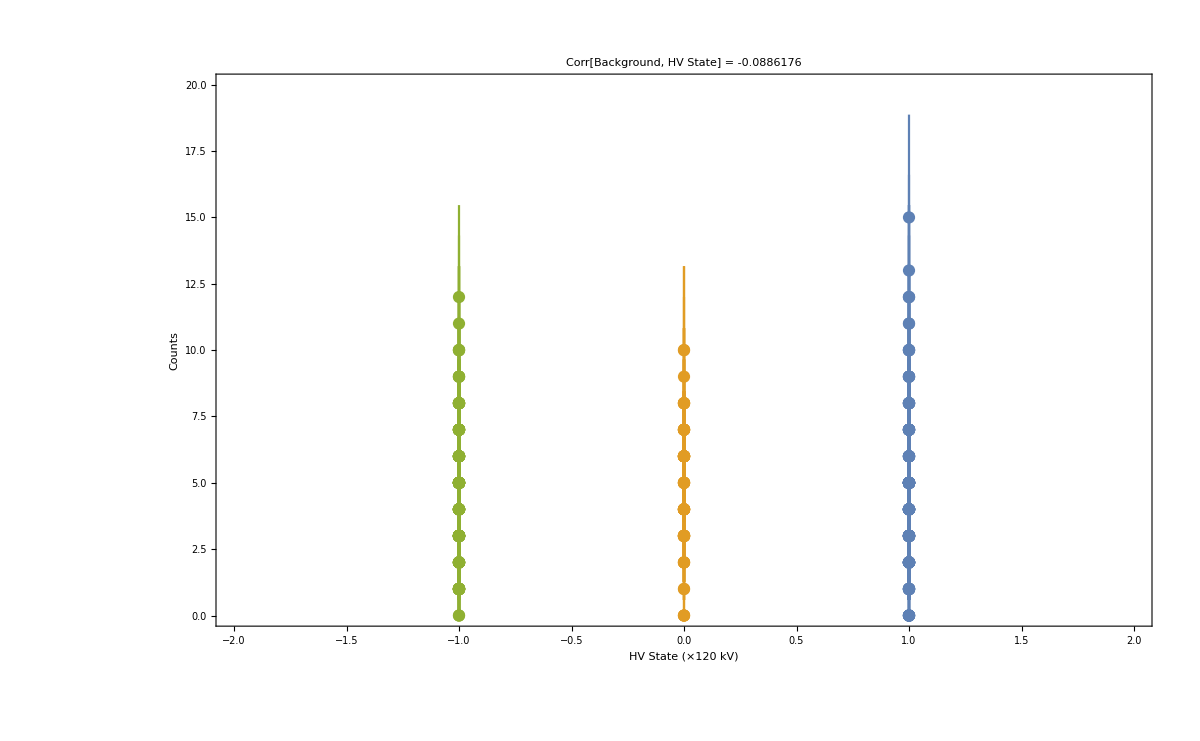

```mathematica
corrbkg=Correlation[Join[Table[{Join[nupp01,nupp02,nupp11,nupp12][[k]],1},{k,1,counupp01+counupp02+counupp11+counupp12}],
Table[{Join[nupz01,nupz02,nupz11,nupz12][[k]],0},{k,1,counupz01+counupz02+counupz11+counupz12}],
Table[{Join[nupn01,nupn02,nupn11,nupn12][[k]],-1},{k,1,counupn01+counupn02+counupn11+counupn12}]][[;;,1]],Join[Table[{Join[nupp01,nupp02,nupp11,nupp12][[k]],1},{k,1,counupp01+counupp02+counupp11+counupp12}],
Table[{Join[nupz01,nupz02,nupz11,nupz12][[k]],0},{k,1,counupz01+counupz02+counupz11+counupz12}],
Table[{Join[nupn01,nupn02,nupn11,nupn12][[k]],-1},{k,1,counupn01+counupn02+counupn11+counupn12}]][[;;,2]]]
EDAListPlot[Table[{1,{Join[nupp01,nupp02,nupp11,nupp12][[k]],Sqrt[Join[nupp01,nupp02,nupp11,nupp12][[k]]]}},{k,1,counupp01+counupp02+counupp11+counupp12}],Table[{0,{Join[nupz01,nupz02,nupz11,nupz12][[k]],Sqrt[Join[nupz01,nupz02,nupz11,nupz12][[k]]]}},{k,1,counupz01+counupz02+counupz11+counupz12}],
Table[{-1,{Join[nupn01,nupn02,nupn11,nupn12][[k]],Sqrt[Join[nupn01,nupn02,nupn11,nupn12][[k]]]}},{k,1,counupn01+counupn02+counupn11+counupn12}],Frame->True,FrameLabel->{Style["HV State (×120 kV)",FontSize->18],Style["Counts",FontSize->18]},TicksStyle->Large,PlotLabel->Style[StringJoin["Corr[Background, HV State] = ",ToString[corrbkg]],FontSize->18],LabelStyle->{18},PlotRange->{{-2,2},{0,20}},ImageSize->1200]
```

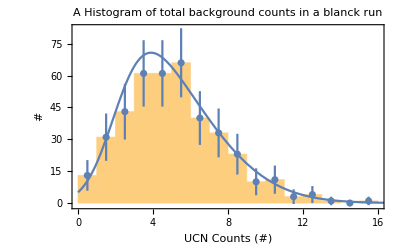

```mathematica
Show[{
Histogram[bkgcouu,Frame->True,FrameLabel->{"UCN Counts (#)","#"},TicksStyle->Directive[FontSize->40],PlotLabel->"A Histogram of total background counts in a blanck run",LabelStyle->{Black,18},ImageSize->{1000}],
Plot[(0.65 Max[HistogramList[bkgcouu][[2]]]/PDF[SkewNormalDistribution[2,4,3],2])PDF[SkewNormalDistribution[2,4,3],x],{x,0,20},Frame->True,FrameLabel->{"UCN Counts (#)","#"},TicksStyle->Directive[FontSize->40],PlotLabel->"A Histogram of total background counts in a blanck run",LabelStyle->{Black,18},ImageSize->{1000}],
EDAListPlot[Table[{k-.5,Transpose[{HistogramList[bkgcouu][[2]],2Sqrt[HistogramList[bkgcouu][[2]]]}][[k]]},{k,1,16}],Frame->True,FrameLabel->{"UCN Counts (#)","#"},TicksStyle->Directive[FontSize->40],PlotLabel->"A Histogram of total background counts in a blanck run",LabelStyle->{Black,18},ImageSize->{1000}]
}]
```

```mathematica
fCalcRamsey[data_,heading_]:=(
rfcoun=Table[{0,0},{k,1,4}];
maxCy=4*Floor[Dimensions[data][[1]]/4];
goodRamsey[xx_]=Abs[Floor[5000 Cos[2 (180+8/π) π (-30.50505691778161+xx)]]];
rfcoun[[1]][[1]]=30.207705; rfcoun[[2]][[1]]=30.207428; rfcoun[[3]][[1]]=30.210158; rfcoun[[4]][[1]]=30.210433;
(*rfcoun[[1]][[1]]=30.207705+RandomReal[.00005]; rfcoun[[2]][[1]]=30.207428+RandomReal[.00005]; rfcoun[[3]][[1]]=30.210158+RandomReal[.00005]; rfcoun[[4]][[1]]=30.210433+RandomReal[.00005];*)
rfcoun[[1]][[2]]=Total[data[[1;;maxCy;;4]]]+954; 
rfcoun[[2]][[2]]=Total[data[[2;;maxCy;;4]]]+2440; 
rfcoun[[3]][[2]]=Total[data[[3;;maxCy;;4]]]+1015; 
rfcoun[[4]][[2]]=Total[data[[4;;maxCy;;4]]]+2484;
errrfcoun={Sqrt[rfcoun[[1]][[2]]],Sqrt[rfcoun[[2]][[2]]],Sqrt[rfcoun[[3]][[2]]],Sqrt[rfcoun[[4]][[2]]]};
rfcouerr={{{rfcoun[[1]][[1]],0.00001},{rfcoun[[1]][[2]],Sqrt[rfcoun[[1]][[2]]]}},{{rfcoun[[2]][[1]],0.00001},{rfcoun[[2]][[2]],Sqrt[rfcoun[[2]][[2]]]}},{{rfcoun[[3]][[1]],0.00001},{rfcoun[[3]][[2]],Sqrt[rfcoun[[3]][[2]]]}},{{rfcoun[[4]][[1]],0.00001},{rfcoun[[4]][[2]],Sqrt[rfcoun[[4]][[2]]]}}};
(**)
Teff=180+8/Pi;
nlm100=NonlinearModelFit[rfcoun,{aa Cos[ 2π(xx-p)Teff]+bb,{p>30.2,p<30.3}},{aa,p,bb},{xx},Weights->1/(errrfcoun^2),Method->{"NMinimize"}];
a1=aa/.nlm100[[1]][[2]];
b1=bb/.nlm100[[1]][[2]];
p1=p/.nlm100[[1]][[2]];
(**)
Print[Show[{Plot[b1+a1 Cos[ 2π(xx-p1)Teff],{xx,30.207,30.2115},Frame->True,FrameLabel->{Style["RF Frequency (Hz)",FontSize->18],Style["Neutron Counts",FontSize->18]},TicksStyle->Large,PlotLabel->Style[heading,FontSize->18],LabelStyle->{18},PlotRange->{{30.207,30.211},{100,3500}}],EDAListPlot[rfcouerr,Frame->True,FrameLabel->{Style["RF Frequency (Hz)",FontSize->18],Style["Neutron Counts",FontSize->18]},TicksStyle->Large,PlotLabel->Style[heading,FontSize->18],LabelStyle->{18},PlotRange->{{30.207,30.211},{100,3500}}]}]];
(**)
{N[p1],Quiet[nlm100["ParameterErrors"]][[2]]}
);
calcFedm[hvp_,hvm_]=(
ee=ElectronCharge/Coulomb;
hp=PlanckConstant/(2 π Joule Second);
eEf=11200;
{(hp SubtractWithError[hvp,hvm])/(4(ee eEf) (10000)^(1/2))}
);
```

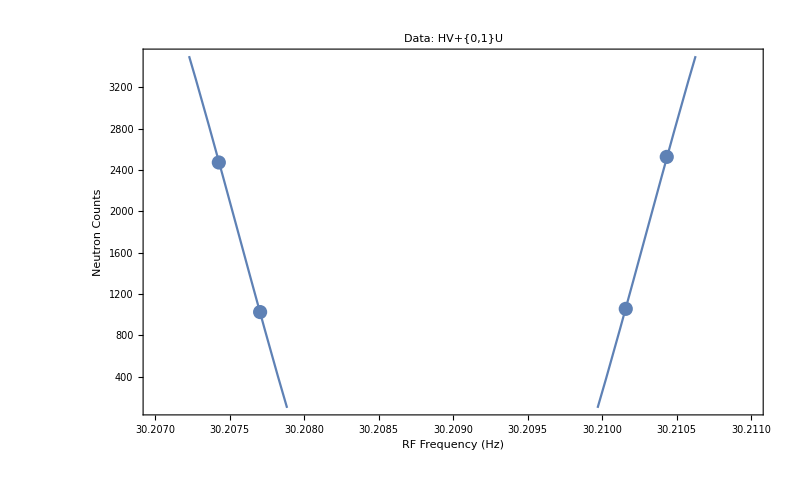

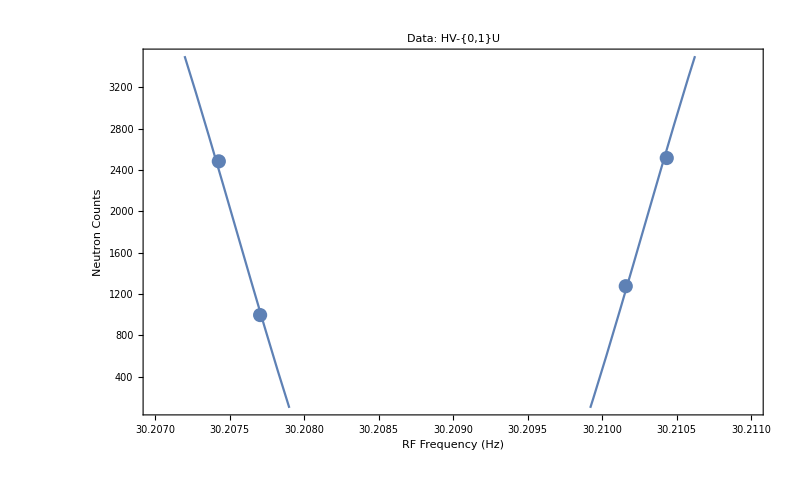

1.76307×10^-27

```mathematica
(*For sf1=0,sf2=1,U*)
calcFedm[fCalcRamsey[Join[nupp01],"Data: HV+{0,1}U"],fCalcRamsey[Join[nupn01],"Data: HV-{0,1}U"]][[1]][[2]]
```

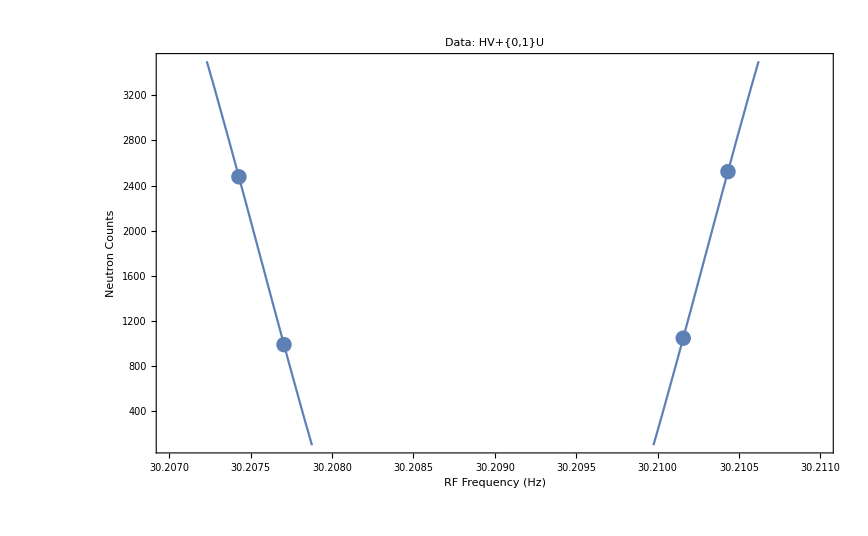

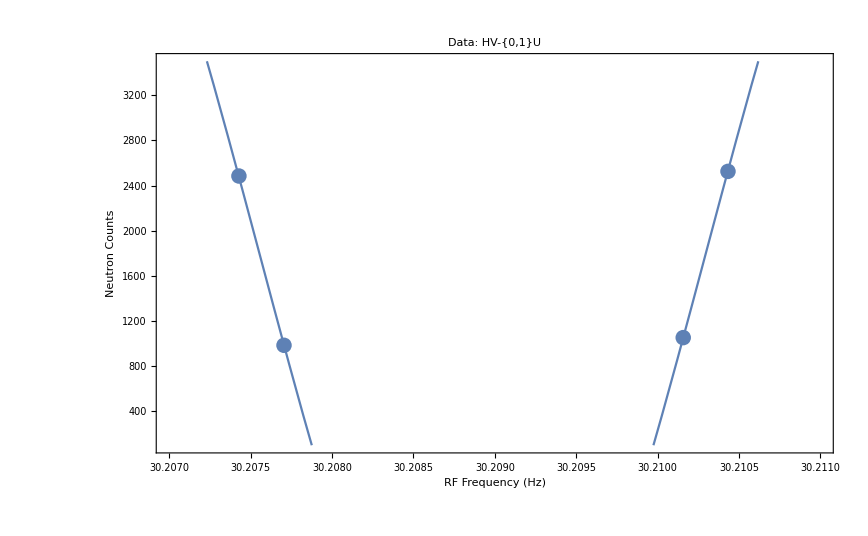

1.1313×10^-28

```mathematica
(*For sf1=1,sf2=1,U*)
calcFedm[fCalcRamsey[Join[nupp12],"Data: HV+{0,1}U"],fCalcRamsey[Join[nupn12],"Data: HV-{0,1}U"]][[1]][[2]]
```

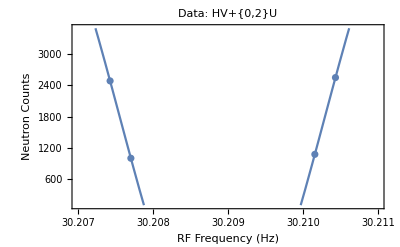

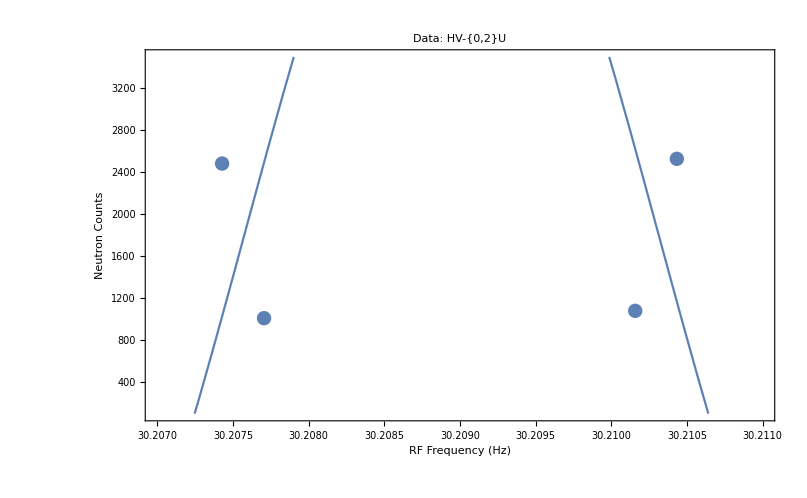

4.11382×10^-26

```mathematica
(*For sf1=0,sf2=2,U*)
calcFedm[fCalcRamsey[Join[nupp02],"Data: HV+{0,2}U"],fCalcRamsey[Join[nupn02],"Data: HV-{0,2}U"]][[1]][[2]]
```

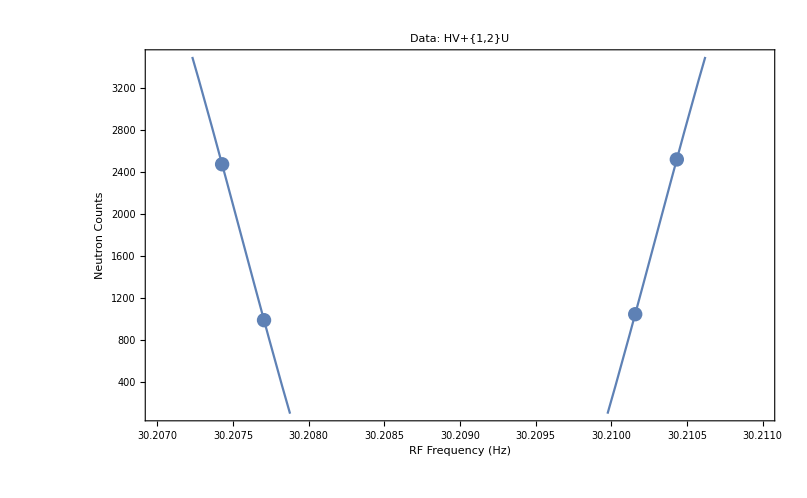

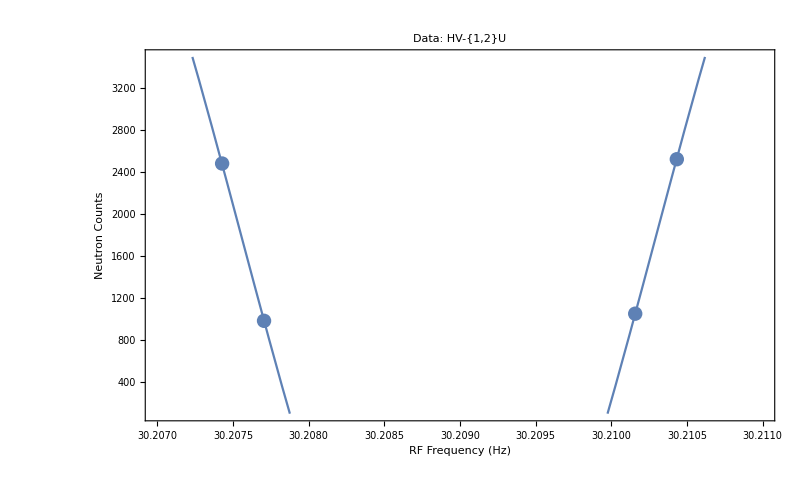

1.1313×10^-28

```mathematica
(*For sf1=1,sf2=2,U*)
calcFedm[fCalcRamsey[Join[nupp12],"Data: HV+{1,2}U"],fCalcRamsey[Join[nupn12],"Data: HV-{1,2}U"]][[1]][[2]]
```

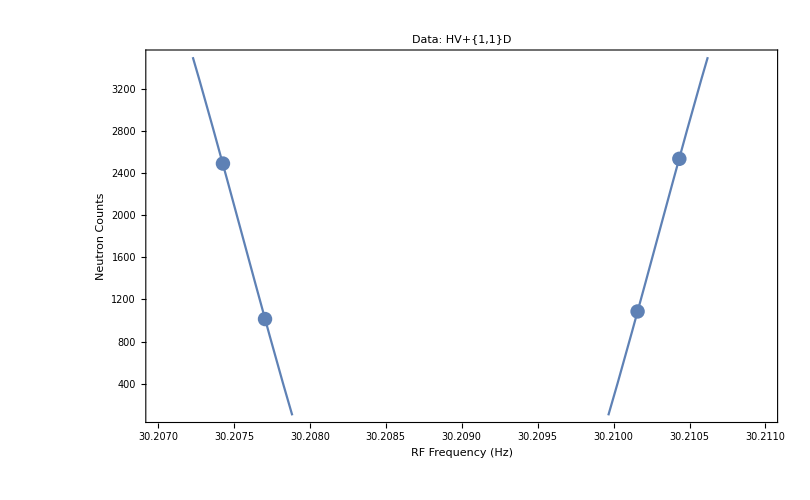

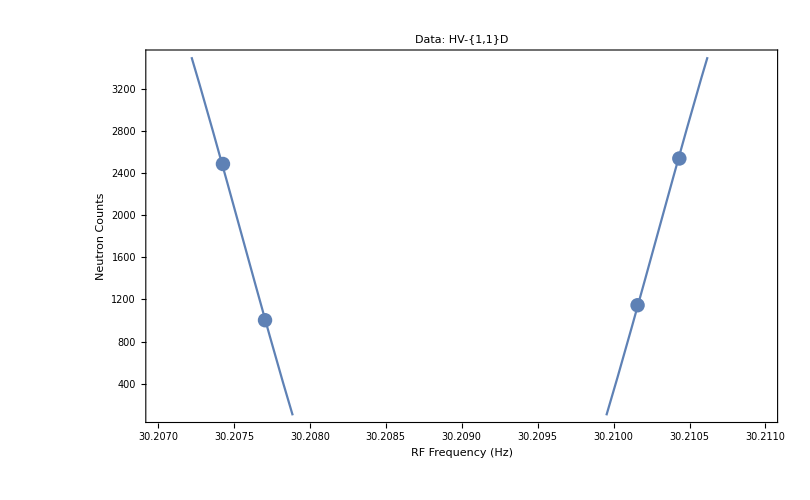

5.2892×10^-28

```mathematica
(*For sf1=0,sf2=1,D*)
calcFedm[fCalcRamsey[Join[ndownp01],"Data: HV+{1,1}D"],fCalcRamsey[Join[ndownn01],"Data: HV-{1,1}D"]][[1]][[2]]
```

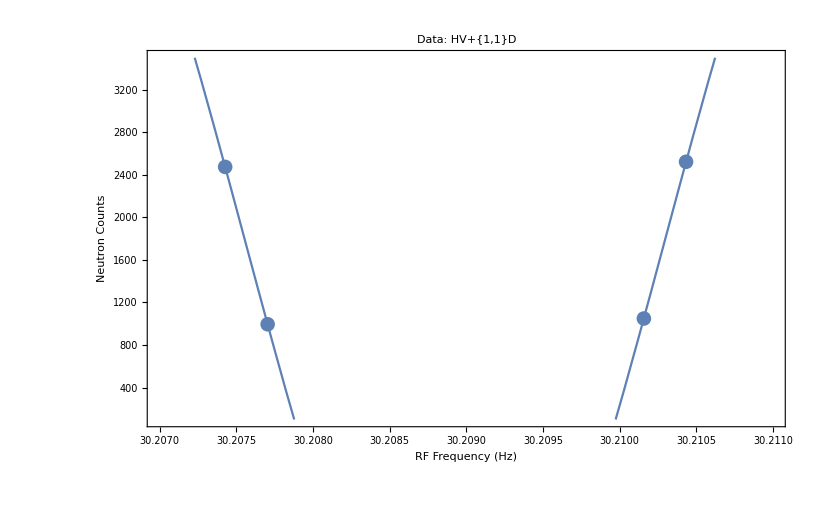

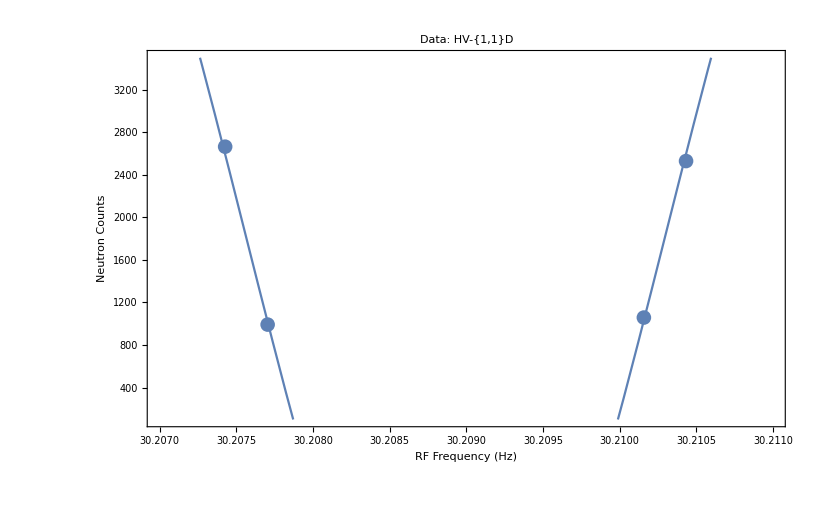

1.11661×10^-27

```mathematica
(*For sf1=1,sf2=1,D*)
calcFedm[fCalcRamsey[Join[ndownp11],"Data: HV+{1,1}D"],fCalcRamsey[Join[ndownn11],"Data: HV-{1,1}D"]][[1]][[2]]
```

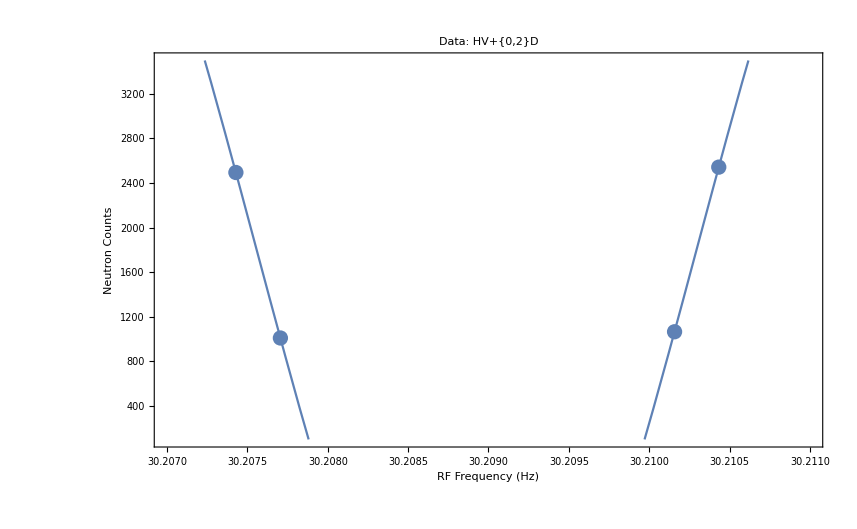

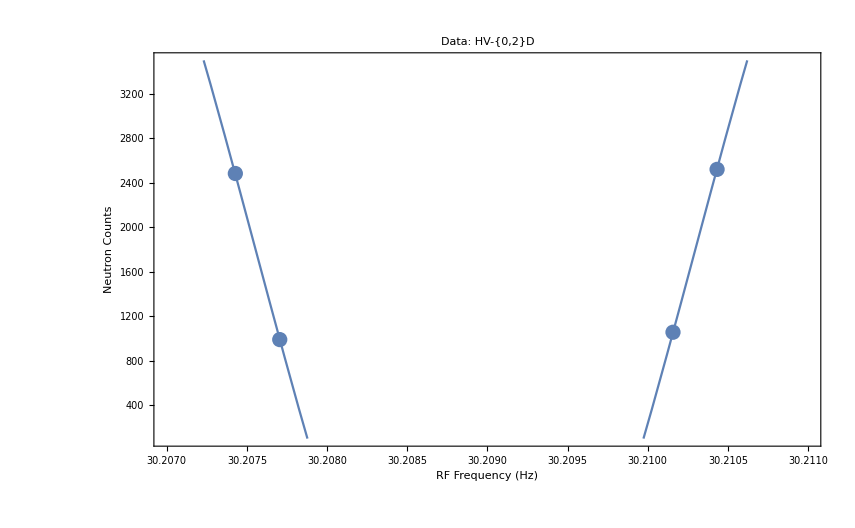

1.21946×10^-28

```mathematica
(*For sf1=0,sf2=2,D*)
calcFedm[fCalcRamsey[Join[ndownp02],"Data: HV+{0,2}D"],fCalcRamsey[Join[ndownn02],"Data: HV-{0,2}D"]][[1]][[2]]
```

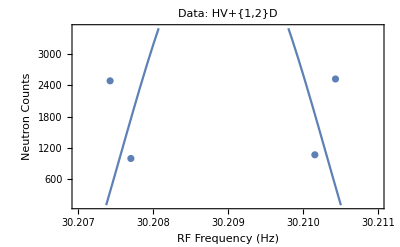

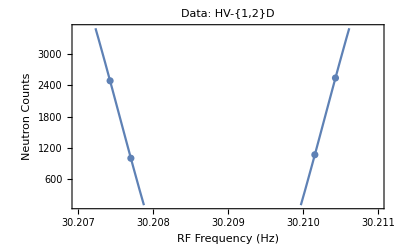

3.81998×10^-26

```mathematica
(*For sf1=1,sf2=2,D*)
calcFedm[fCalcRamsey[Join[ndownp12],"Data: HV+{1,2}D"],fCalcRamsey[Join[ndownn12],"Data: HV-{1,2}D"]][[1]][[2]]
```

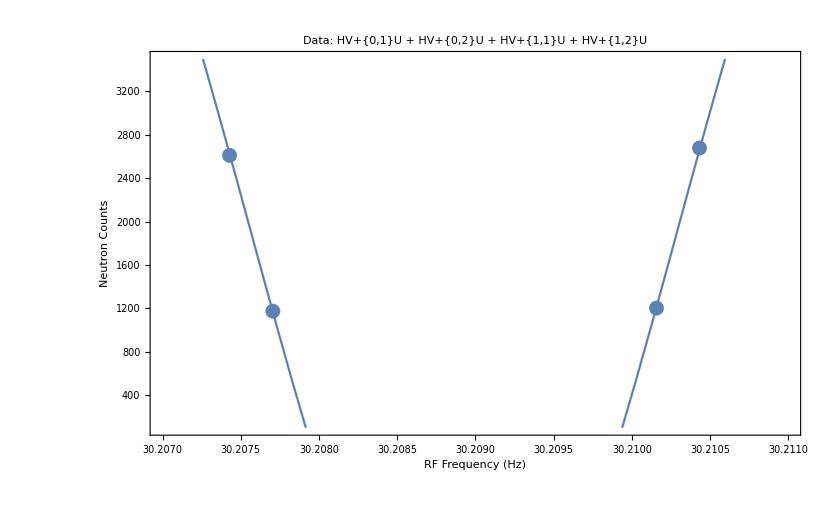

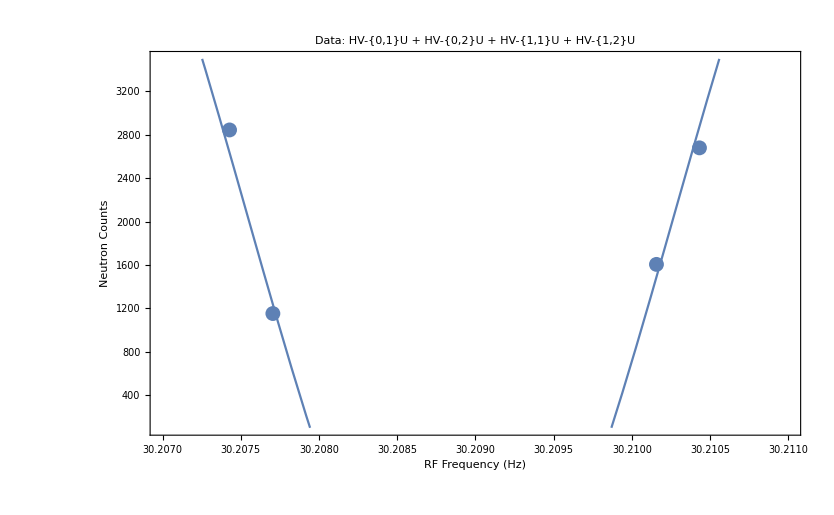

4.40767×10^-27

```mathematica
(*For Global*)
calcFedm[fCalcRamsey[Join[nupp02,nupp01,nupp11,nupp12],"Data: HV+{0,1}U + HV+{0,2}U + HV+{1,1}U + HV+{1,2}U"],fCalcRamsey[Join[nupn02,nupn01,nupn11,nupn12],"Data: HV-{0,1}U + HV-{0,2}U + HV-{1,1}U + HV-{1,2}U"]][[1]][[2]]
```

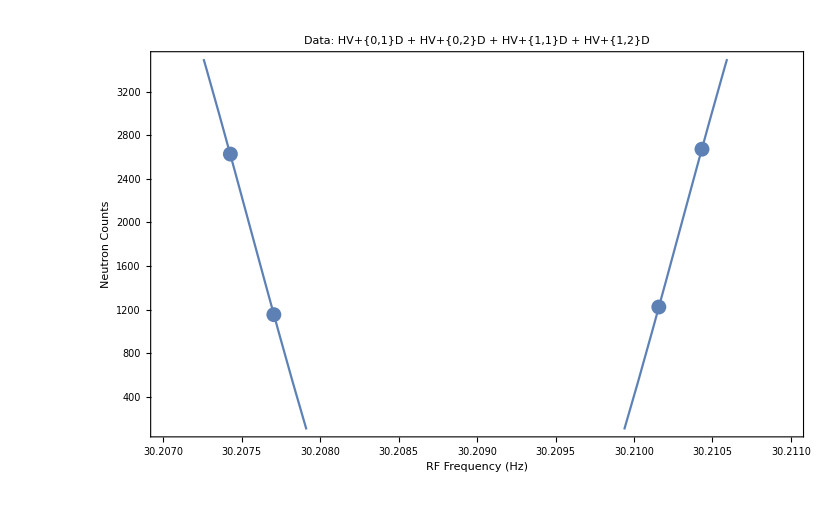

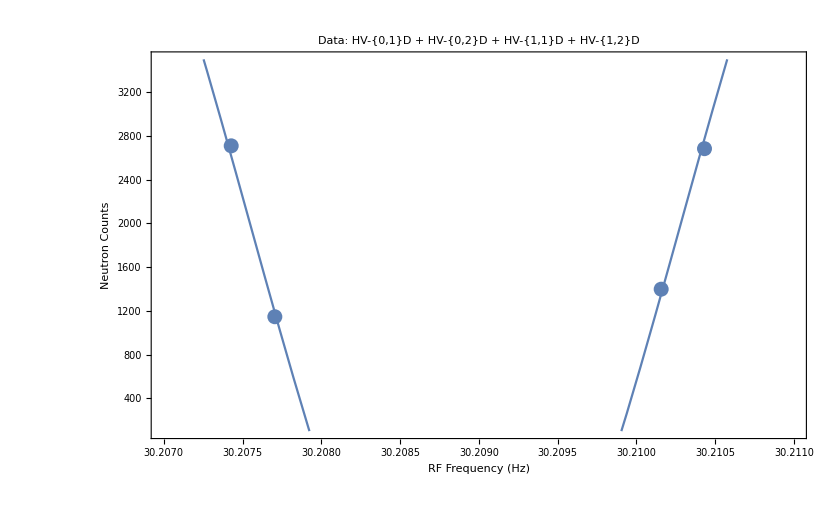

1.76307×10^-27

```mathematica
calcFedm[fCalcRamsey[Join[ndownp02,ndownp01,ndownp11,ndownp12],"Data: HV+{0,1}D + HV+{0,2}D + HV+{1,1}D + HV+{1,2}D"],fCalcRamsey[Join[ndownn02,ndownn01,ndownn11,ndownn12],"Data: HV-{0,1}D + HV-{0,2}D + HV-{1,1}D + HV-{1,2}D"]][[1]][[2]]
```